# Finite Length Solenoid Field

```mathematica
x={ρ,0,z}
X={a Cos[ϕ],a Sin[ϕ],k}
```

{ρ,0,z}

{a Cos[ϕ],a Sin[ϕ],k}

```mathematica
(x-X).(x-X)//FullSimplify
```

a^2+(k-z)^2+ρ^2-2 a ρ Cos[ϕ]

## Single Coil

```mathematica
Integrate[1/(√(a^2+(k-z)^2+ρ^2-2 a ρ Cos[ϕ])),k]
```

Log[k-z+√(a^2+(k-z)^2+ρ^2-2 a ρ Cos[ϕ])]

```mathematica
K=Integrate[Cos[2ϕ]/(√(ζ^2+(a+ρ)^2-4 a ρ Sin[ϕ]^2)),ϕ] (* ϕ∈(0,π), ζ=k-z *);
```

```mathematica
(K/.ϕ->π)-(K/.ϕ->0)//FullSimplify
```

(2 (ζ^2+(a+ρ)^2) EllipticE[(4 a ρ)/(ζ^2+(a+ρ)^2)]-2 (a^2+ζ^2+ρ^2) EllipticK[(4 a ρ)/(ζ^2+(a+ρ)^2)])/(2 a ρ √(ζ^2+(a+ρ)^2))

```mathematica
Simplify[(2 (ζ^2+(a+ρ)^2) EllipticE[(4 a ρ)/(ζ^2+(a+ρ)^2)]-2 (a^2+ζ^2+ρ^2) EllipticK[(4 a ρ)/(ζ^2+(a+ρ)^2)])/(2 a ρ √(ζ^2+(a+ρ)^2))/.{ζ^2+(a+ρ)^2->(4 a ρ)/k^2,a^2+ζ^2+ρ^2-> (4 a ρ)/k^2-2a ρ},{k>0}]
```

(2 EllipticE[k^2]+(-2+k^2) EllipticK[k^2])/(k √(a ρ))

```mathematica
AϕSC[a_,z_,ρ_,ζ_]:=(√((ζ-z)^2+(a+ρ)^2))/ρ (EllipticE[(4 a ρ)/((ζ-z)^2+(a+ρ)^2)]- (a^2+(ζ-z)^2+ρ^2)/((ζ-z)^2+(a+ρ)^2) EllipticK[(4 a ρ)/((ζ-z)^2+(a+ρ)^2)])
```

```mathematica
BρSC[a_,z_,ρ_,ζ_]:=(z-ζ)/(ρ √((z-ζ)^2+(a+ρ)^2))(EllipticK[(4 a ρ)/((ζ-z)^2+(a+ρ)^2)]- (a^2+ρ^2+(ζ-z)^2)/((a-ρ)^2+(ζ-z)^2) EllipticE[(4 a ρ)/((ζ-z)^2+(a+ρ)^2)])
BζSC[a_,z_,ρ_,ζ_]:=If[ρ>0,1/(√((ζ-z)^2+(a+ρ)^2))( EllipticK[(4 a ρ)/((ζ-z)^2+(a+ρ)^2)]+(a^2-ρ^2-(ζ-z)^2)/((a-ρ)^2+(ζ-z)^2) EllipticE[(4 a ρ)/((ζ-z)^2+(a+ρ)^2)] ),(a^2 π)/((a^2+(z-ζ)^2)^(3/2))]
```

```mathematica
Limit[BρSC[a,0,ρ,ζ],ρ->0]
Limit[BζSC[a,0,ρ,ζ],ρ->0]
Limit[BζSC[a,0,ρ,ζ],ζ->0]
```

0

(a^2 π)/((a^2+ζ^2)^(3/2))

Piecewise[{{(√(a^2) π)/a^2, ρ≤0}, {((a+ρ) EllipticE[(4 a ρ)/(a+ρ)^2]+(a-ρ) EllipticK[(4 a ρ)/(a+ρ)^2])/((a-ρ) √((a+ρ)^2)), True}}]

```mathematica
Manipulate[Plot[BζSC[a,0,ρ,ζ],{ρ,0,4},PlotRange->4],{a,0.5,4.5},{ζ,0,4}]
```

```mathematica
Displayfield[a_,z_]:=StreamDensityPlot[{BρSC[a,z,R,Z],BζSC[a,z,Abs[R],Z]},{R,-2,2},{Z,-2,2},StreamPoints->Fine, StreamColorFunction->"Rainbow",ColorFunction->Hue,ImageSize->500]
DisplayfieldM[a_,z_,n_,d_,p_]:=Show[
StreamDensityPlot[
Sum[{ BρSC[a,z+m d,R,Z],BζSC[a,z+m d,Abs[R],Z]},{m,0,n-1,1}]
,{R,-18,18},{Z,-18,18},StreamPoints->p, StreamColorFunction->"Rainbow",ColorFunction->Hue,ImageSize->500],
Graphics[Circle[{0,0},7]]
]
```

```mathematica
Displayfield[1,0]
```

-Graphics-

```mathematica
DisplayfieldM[27,-15,2,30,3000]
```

-Graphics-

```mathematica
DisplayfieldM[15,-15,2,30,3000]
```

-Graphics-

```mathematica
DisplayfieldM[7,-15,2,30,3000]
```

-Graphics-

```mathematica
Plot3D[Norm[{ BρSC[15,15,R,Z],BζSC[15,15,Abs[R],Z]}]+Norm[{ BρSC[15,-15,R,Z],BζSC[15,-15,Abs[R],Z]}]
,{R,-18,18},{Z,-18,18},PlotPoints->100,ImageSize->500(*, RegionFunction->Function[{x,y},0<x^2+y^2<49],PlotRange->{0,0.2}*)]
```

-Graphics3D-

```mathematica
Plot3D[Norm[{ BρSC[15,15,R,Z],BζSC[15,15,Abs[R],Z]}]+Norm[{ BρSC[15,-15,R,Z],BζSC[15,-15,Abs[R],Z]}]
,{R,-18,18},{Z,-18,18},PlotPoints->200,ImageSize->500, RegionFunction->Function[{x,y},0<x^2+y^2<49],PlotRange->{0,0.3}]
```

-Graphics3D-

```mathematica
Aϕ[a_,z_,ρ_,ζ_]:=(√((ζ-z)^2+(a+ρ)^2))/ρ (EllipticE[(4 a ρ)/((ζ-z)^2+(a+ρ)^2)]- (a^2+(ζ-z)^2+ρ^2)/((ζ-z)^2+(a+ρ)^2) EllipticK[(4 a ρ)/((ζ-z)^2+(a+ρ)^2)])
```

```mathematica
Plot3D[ Aϕ[1,0,R,k],{R,0,2},{k,0,2}(*FrameLabel->Automatic,Contours->30,*)(*,Exclusions->{R==0 }*)]
```

-Graphics3D-

```mathematica
Table[-0.5n,{n,0,9}]
```

{0.,0.5,1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.,5.5,6.,6.5,7.,7.5,8.,8.5,9.,9.5,10.,10.5,11.,11.5,12.,12.5,13.,13.5,14.,14.5,15.,15.5,16.,16.5,17.,17.5,18.,18.5,19.,19.5,20.}

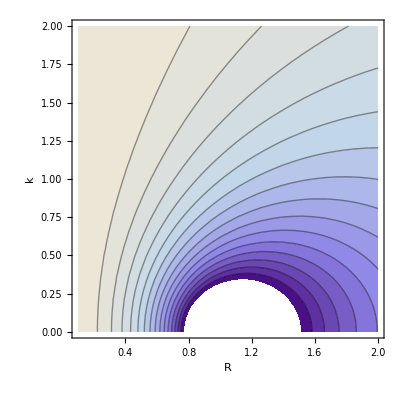

```mathematica
ContourPlot[2π R Aϕ[1,0,R,k],{R,0.1,2},{k,0,2},FrameLabel->Automatic,PlotRange->8,Contours->Table[-0.5n,{n,0,15}]]
```

```mathematica
L[R_,h_,k_]:=NIntegrate[R Aϕ[1,0,√(R^2+h^2+2R h Cos[θ]),k],{θ,0,2π}]
```

```mathematica
L[2,0,0]
2π 2 Aϕ[1,0,2,0]//N
```

-5.48618

-5.48618

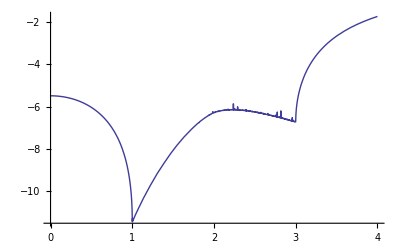

```mathematica
Plot[L[2,h,0],{h,0,4}]
```

```mathematica
Plot3D[L[2,h,k],{h,0,4},{k,0,2},BoxRatios->{10,5,5}]
```

-Graphics3D-

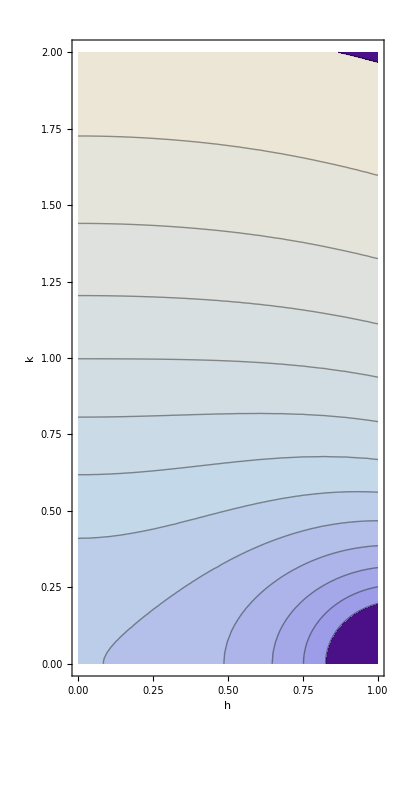

```mathematica
ContourPlot[L[2,h,k],{h,0,1},{k,0,2},FrameLabel->Automatic, Contours->Table[-0.5n,{n,0,15}],AspectRatio->2]
```

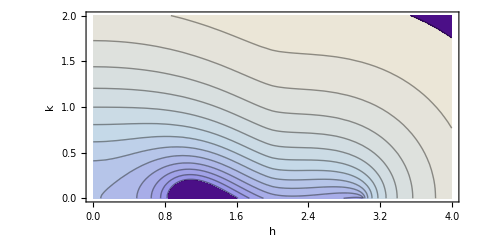

```mathematica
ContourPlot[L[2,h,k],{h,0,4},{k,0,2},FrameLabel->Automatic, Contours->Table[-0.5n,{n,0,15}],AspectRatio->0.5]
```

```mathematica
Integrate[EllipticK[k],k]//Simplify
```

2 (EllipticE[k]+(-1+k) EllipticK[k])

## Finite Coil

### Analytic Form

```mathematica
Collect[FullSimplify[(*(μ0 i)/(4π L)*)√(a/ρ)(z-L/2)(-EllipticE[(4 a ρ)/((a+ρ)^2+(z-L/2)^2)]/k+((h^2+((4 a ρ)/((a+ρ)^2+(z-L/2)^2))-h^2 ((4 a ρ)/((a+ρ)^2+(z-L/2)^2))) EllipticK[(4 a ρ)/((a+ρ)^2+(z-L/2)^2)])/(h^2 k)+((-1+h^2) k EllipticPi[h^2,(4 a ρ)/((a+ρ)^2+(z-L/2)^2)])/h^2)/.{h->(2 √(a ρ))/(a+ρ),k->(2 √(a ρ))/(√((a+ρ)^2+(z-L/2)^2))},{a>0,ρ>0}],{EllipticK[k^2],EllipticE[k^2],EllipticPi[h^2,k^2]}]
```

1/(8 √(ρ^2 ((L-2 z)^2+4 (a+ρ)^2)))(L-2 z) (((L-2 z)^2+4 (a+ρ)^2) EllipticE[(4 a ρ)/((-L/2+z)^2+(a+ρ)^2)]-(8 a^2+(L-2 z)^2+8 ρ^2) EllipticK[(4 a ρ)/((-L/2+z)^2+(a+ρ)^2)]+4 (a-ρ)^2 EllipticPi[(4 a ρ)/(a+ρ)^2,(4 a ρ)/((-L/2+z)^2+(a+ρ)^2)])

```mathematica
Aup[a_,L_,ρ_,z_]:=1/(8 ρ √((L-2 z)^2+4 (a+ρ)^2))(L-2 z) (((L-2 z)^2+4 (a+ρ)^2) EllipticE[(4 a ρ)/((-L/2+z)^2+(a+ρ)^2)]-(8 a^2+(L-2 z)^2+8 ρ^2) EllipticK[(4 a ρ)/((-L/2+z)^2+(a+ρ)^2)]+4 (a-ρ)^2 EllipticPi[(4 a ρ)/(a+ρ)^2,(4 a ρ)/((-L/2+z)^2+(a+ρ)^2)])
```

```mathematica
Aϕ[a_,L_,ρ_,z_]:=(*(μ0 M)/(4π)*)(Aup[a,L/2,ρ,z]-Aup[a,-L/2,ρ,z])
```

```mathematica
Collect[-D[Aup[a,L,ρ,z],z]//FullSimplify,{EllipticK[(4 a ρ)/((-L/2+z)^2+(a+ρ)^2)],EllipticE[(4 a ρ)/((-L/2+z)^2+(a+ρ)^2)]}]
Collect[-D[Aup[a,-L,ρ,z],z]//FullSimplify,{EllipticK[(4 a ρ)/((-L/2+z)^2+(a+ρ)^2)],EllipticE[(4 a ρ)/((-L/2+z)^2+(a+ρ)^2)]}]
```

(√((L-2 z)^2+4 (a+ρ)^2) EllipticE[(4 a ρ)/((-L/2+z)^2+(a+ρ)^2)])/(2 ρ)+((-4 a^2-(L-2 z)^2-4 ρ^2) EllipticK[(4 a ρ)/((-L/2+z)^2+(a+ρ)^2)])/(2 ρ √((L-2 z)^2+4 (a+ρ)^2))

(((L+2 z)^2+4 (a+ρ)^2) EllipticE[(4 a ρ)/((L/2+z)^2+(a+ρ)^2)]-(4 a^2+(L+2 z)^2+4 ρ^2) EllipticK[(4 a ρ)/((L/2+z)^2+(a+ρ)^2)])/(2 ρ √((L+2 z)^2+4 (a+ρ)^2))

```mathematica
Simplify[(√((L-2 z)^2+4 (a+ρ)^2) EllipticE[(4 a ρ)/((-L/2+z)^2+(a+ρ)^2)])/(2 ρ)+((-4 a^2-(L-2 z)^2-4 ρ^2) EllipticK[(4 a ρ)/((-L/2+z)^2+(a+ρ)^2)])/(2 ρ √((L-2 z)^2+4 (a+ρ)^2))/.{(L-2 z)^2+4 (a+ρ)^2->(16a ρ)/k^2,(4 a ρ)/((-L/2+z)^2+(a+ρ)^2)->k^2,(L-2 z)^2->(16a ρ)/k^2-4 (a+ρ)^2},{a>0,ρ>0,k>0}]
```

(a (2 EllipticE[k^2]+(-2+k^2) EllipticK[k^2]))/(k √(a ρ))

```mathematica
Collect[1/ρ D[ρ Aup[a,L,ρ,z],ρ]//FullSimplify,{EllipticK[(4 a ρ)/((-L/2+z)^2+(a+ρ)^2)],EllipticE[(4 a ρ)/((-L/2+z)^2+(a+ρ)^2)],EllipticPi[(4 a ρ)/(a+ρ)^2,(4 a ρ)/((-L/2+z)^2+(a+ρ)^2)]}]
Collect[1/ρ D[ρ Aup[a,-L,ρ,z],ρ]//FullSimplify,{EllipticK[(4 a ρ)/((-L/2+z)^2+(a+ρ)^2)],EllipticE[(4 a ρ)/((-L/2+z)^2+(a+ρ)^2)],EllipticPi[(4 a ρ)/(a+ρ)^2,(4 a ρ)/((-L/2+z)^2+(a+ρ)^2)]}]
```

-((L-2 z) EllipticK[(4 a ρ)/((-L/2+z)^2+(a+ρ)^2)])/(√((L-2 z)^2+4 (a+ρ)^2))-((L-2 z) (a-ρ) EllipticPi[(4 a ρ)/(a+ρ)^2,(4 a ρ)/((-L/2+z)^2+(a+ρ)^2)])/((a+ρ) √((L-2 z)^2+4 (a+ρ)^2))

((L+2 z) ((a+ρ) EllipticK[(4 a ρ)/((L/2+z)^2+(a+ρ)^2)]+(a-ρ) EllipticPi[(4 a ρ)/(a+ρ)^2,(4 a ρ)/((L/2+z)^2+(a+ρ)^2)]))/((a+ρ) √((L+2 z)^2+4 (a+ρ)^2))

```mathematica
Simplify[-((L-2 z) EllipticK[(4 a ρ)/((-L/2+z)^2+(a+ρ)^2)])/(√((L-2 z)^2+4 (a+ρ)^2))-((L-2 z) (a-ρ) EllipticPi[(4 a ρ)/(a+ρ)^2,(4 a ρ)/((-L/2+z)^2+(a+ρ)^2)])/((a+ρ) √((L-2 z)^2+4 (a+ρ)^2))/.{(L-2 z)^2+4 (a+ρ)^2->(16a ρ)/k^2,(4 a ρ)/((-L/2+z)^2+(a+ρ)^2)->k^2,(L-2 z)^2->(16a ρ)/k^2-4 (a+ρ)^2},{a>0,ρ>0,k>0}]
```

-(k (L-2 z) ((a+ρ) EllipticK[k^2]+(a-ρ) EllipticPi[(4 a ρ)/(a+ρ)^2,k^2]))/(4 √(a ρ) (a+ρ))

```mathematica
Bρ[a_,L_,ρ_,z_]:=(*(μ0 M)/(4π)*)(((√((L-2 z)^2+4 (a+ρ)^2) EllipticE[(4 a ρ)/((-L/2+z)^2+(a+ρ)^2)])/(2 ρ)+((-4 a^2-(L-2 z)^2-4 ρ^2) EllipticK[(4 a ρ)/((-L/2+z)^2+(a+ρ)^2)])/(2 ρ √((L-2 z)^2+4 (a+ρ)^2)))-((((L+2 z)^2+4 (a+ρ)^2) EllipticE[(4 a ρ)/((L/2+z)^2+(a+ρ)^2)]-(4 a^2+(L+2 z)^2+4 ρ^2) EllipticK[(4 a ρ)/((L/2+z)^2+(a+ρ)^2)])/(2 ρ √((L+2 z)^2+4 (a+ρ)^2))))
Bx[a_,L_,ρ_,z_]:=(*(μ0 i)/(4π)*)((-(L-2 z)/(√((L-2 z)^2+4 (a+ρ)^2))(EllipticK[(4 a ρ)/((-L/2+z)^2+(a+ρ)^2)]+(a-ρ)/(a+ρ)EllipticPi[(4 a ρ)/(a+ρ)^2,(4 a ρ)/((-L/2+z)^2+(a+ρ)^2)]))-((L+2 z)/(√((L+2 z)^2+4 (a+ρ)^2)) (EllipticK[(4 a ρ)/((L/2+z)^2+(a+ρ)^2)]+(a-ρ)/(a+ρ) EllipticPi[(4 a ρ)/(a+ρ)^2,(4 a ρ)/((L/2+z)^2+(a+ρ)^2)])))
```

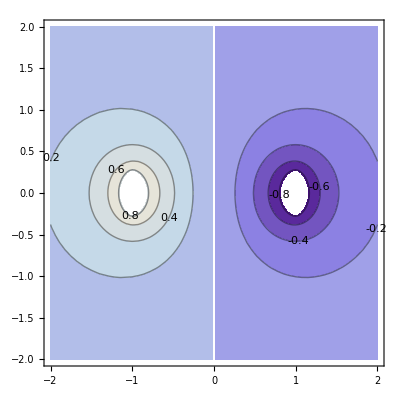

```mathematica
Show[
ContourPlot[Aϕ[1,1,R,Z],{R,-2,2},{Z,-2,2},Contours->Table[0.2n,{n,-15,15}],ContourLabels->True,Exclusions->{R==0}],
DrawRec[1,1]
]
```

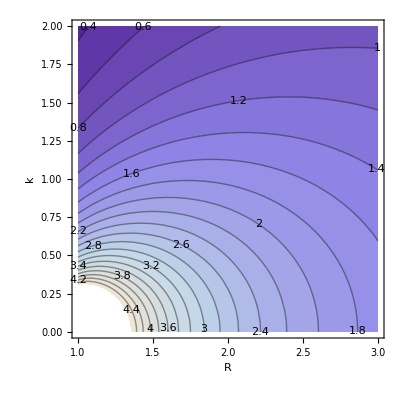

```mathematica
ContourPlot[-2π R Aϕ[1,1,R,k],{R,1,3},{k,0,2},Contours->Table[0.2n,{n,0,40}],ContourLabels->True,FrameLabel->Automatic]
```

```mathematica
ContourPlot3D[-2π R (Aup[1,L/2,R,k]-Aup[1,-L/2,R,k]),{R,1,3},{k,0,2},{L,0.2,2},PlotPoints->6, Contours->Table[n,{n,0,20}]]
```

-Graphics3D-

```mathematica
DrawRec[a_,L_]:=Graphics[{EdgeForm[Thin],Transparent,Rectangle[{-a,-L/2},{a,L/2}]}]
Field[a_,L_]:=Show[
StreamDensityPlot[{-Bρ[a,L,R,Z],-Bx[a,L,R,Z]},{R,-2,2},{Z,-2,2}, StreamColorFunction->"Rainbow",ColorFunction->Hue,ImageSize->500,StreamPoints->Fine],
DrawRec[a,L]
]
```

```mathematica
Field[1,1]
```

-Graphics-

```mathematica
Field[1,0.2]
```

-Graphics-

```mathematica
Field[0.5,3]
```

-Graphics-

### Numerical Integration

```mathematica
AϕL[a_,L_,ρ_,z_]:=(*(μ0 i)/(2π)*)1/L NIntegrate[(√(ζ^2+(a+ρ)^2))/ρ (EllipticE[(4 a ρ)/(ζ^2+(a+ρ)^2)]- (ζ^2+a^2+ρ^2)/(ζ^2+(a+ρ)^2) EllipticK[(4 a ρ)/(ζ^2+(a+ρ)^2)]),{ζ,z-L/2,z+L/2}]
```

```mathematica
(* or *)
AϕL2[a_,L_,ρ_,z_]:=(*(μ0 i)/(2π)*)(a^2 ρ)/L NIntegrate[ Sin[θ]^2((z-L/2)/((a^2+ρ^2-2a ρ Cos[θ])√(a^2+ρ^2+(z-L/2)^2-2a ρ Cos[θ]))-(z+L/2)/((a^2+ρ^2-2a ρ Cos[θ])√(a^2+ρ^2+(z+L/2)^2-2a ρ Cos[θ]))),{θ,0,π}]
```

```mathematica
Λ0[θ_,α_]:=EllipticF[θ,Sin[π/2-α]^2]/EllipticK[Sin[π/2-α]^2]+2/π EllipticK[Sin[α]^2]JacobiZeta[θ,Sin[α]^2]
Π[n_,k_]:=EllipticK[k]+π/2 √(n/(1-n)1/(n-k^2))(1-Λ0[ArcSin[√((1-n)/(1-k^2))],k])
```

```mathematica
Bρ[a_,L_,ρ_,z_]:=(*(μ0 i)/(2π)*)-1/L((√((z-L/2)^2+(a+ρ)^2))/ρ (EllipticE[(4 a ρ)/((z-L/2)^2+(a+ρ)^2)]- ((z-L/2)^2+a^2+ρ^2)/((z-L/2)^2+(a+ρ)^2) EllipticK[(4 a ρ)/((z-L/2)^2+(a+ρ)^2)])-(√((z+L/2)^2+(a+ρ)^2))/ρ (EllipticE[(4 a ρ)/((z+L/2)^2+(a+ρ)^2)]- ((z+L/2)^2+a^2+ρ^2)/((z+L/2)^2+(a+ρ)^2) EllipticK[(4 a ρ)/((z+L/2)^2+(a+ρ)^2)]))
Bρ2[a_,L_,ρ_,z_]:=(*(μ0 i)/(2π)*)1/L NIntegrate[-ζ/(ρ √(ζ^2+(a+ρ)^2))(EllipticK[(4 a ρ)/(ζ^2+(a+ρ)^2)]- (a^2+ρ^2+ζ^2)/((a-ρ)^2+ζ^2) EllipticE[(4 a ρ)/(ζ^2+(a+ρ)^2)]),{ζ,z-L/2,z+L/2}]
Bz[a_,L_,ρ_,z_?NumberQ]:=(*(μ0 i)/(2π)*)1/L NIntegrate[1/(√(ζ^2+(a+ρ)^2))( EllipticK[(4 a ρ)/(ζ^2+(a+ρ)^2)]+(a^2-ρ^2-ζ^2)/((a-ρ)^2+ζ^2) EllipticE[(4 a ρ)/(ζ^2+(a+ρ)^2)] ),{ζ,z-L/2,z+L/2}]
```

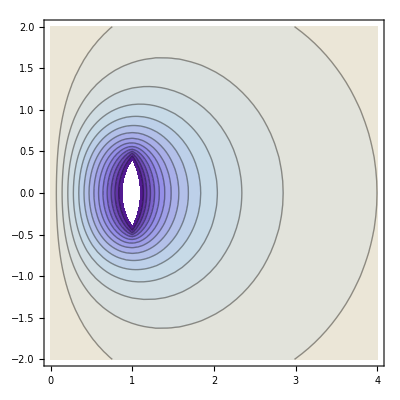

```mathematica
ContourPlot[AϕL[1,1,R,Z],{R,0,4},{Z,-2,2},PlotRange->1.5,Contours->Table[-n 0.1,{n,0,15}],Exclusions->{R==0}]
```

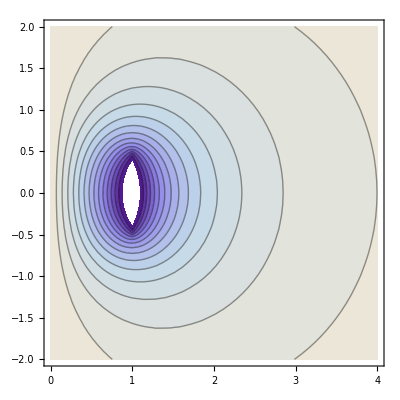

```mathematica
ContourPlot[AϕL2[1,1,R,Z],{R,0,4},{Z,-2,2},PlotRange->1.5,Contours->Table[-n 0.1,{n,0,15}],Exclusions->{R==0}]
```

```mathematica
DrawRec[a_,L_]:=Graphics[{EdgeForm[Thin],Transparent,Rectangle[{-a,-L/2},{a,L/2}]}]
Field[a_?NumberQ,L_?NumberQ]:=Show[
StreamDensityPlot[{Bρ[a,L,R,Z],Bz[a,L,Abs[R],Z]},{R,-2,2},{Z,-2,2}, StreamColorFunction->"Rainbow",ColorFunction->Hue,ImageSize->500,StreamPoints->Fine],
DrawRec[a,L]
]
Field2[a_?NumberQ,L_?NumberQ]:=Show[
StreamDensityPlot[{Bρ2[a,L,R,Z],Bz[a,L,Abs[R],Z]},{R,-2,2},{Z,-2,2}, StreamColorFunction->"Rainbow",ColorFunction->Hue,ImageSize->500,StreamPoints->Fine],
DrawRec[a,L]
]
```

```mathematica
Show[
StreamDensityPlot[{Bρ2[1,1,R,Z],Bz[1,1,Abs[R],Z]},{R,-2,2},{Z,-2,2}, StreamColorFunction->"Rainbow",ColorFunction->Hue,ImageSize->500],
DrawRec[1,1]
]
```

-Graphics-

```mathematica
Show[
StreamDensityPlot[{Bρ[1,0.2,R,Z],Bz[1,0.2,Abs[R],Z]},{R,-2,2},{Z,-2,2}, StreamColorFunction->"Rainbow",ColorFunction->Hue,ImageSize->500],
DrawRec[1,0.2]
]
Show[
StreamDensityPlot[{Bρ2[1,0.2,R,Z],Bz[1,0.2,Abs[R],Z]},{R,-2,2},{Z,-2,2}, StreamColorFunction->"Rainbow",ColorFunction->Hue,ImageSize->500],
DrawRec[1,0.2]
]
```

-Graphics-

-Graphics-

```mathematica
Field[0.5,2]
Field2[0.5,2]
```

-Graphics-

-Graphics-

```mathematica
Clear[R,Z]
```

```mathematica
Field[1,3]
```

-Graphics-

```mathematica
Show[
StreamDensityPlot[{Bρ[2,3,R,Z],Bz[2,3,Abs[R],Z]},{R,-2,2},{Z,-2,2}, StreamColorFunction->"Rainbow",ColorFunction->Hue,ImageSize->500],
DrawRec[2,3]
]
```

-Graphics-

```mathematica
(* ON axis mutual inductance *)
AϕL[a_,L_,ρ_,z_?NumberQ]:=(*(μ0 i)/(2π)*)1/L NIntegrate[(√(ζ^2+(a+ρ)^2))/ρ (EllipticE[(4 a ρ)/(ζ^2+(a+ρ)^2)]- (ζ^2+a^2+ρ^2)/(ζ^2+(a+ρ)^2) EllipticK[(4 a ρ)/(ζ^2+(a+ρ)^2)]),{ζ,z-L/2,z+L/2}]
```

```mathematica
MutualL[a_,L_,R_,k_]:=2π R AϕL[a,L,R,k]
```

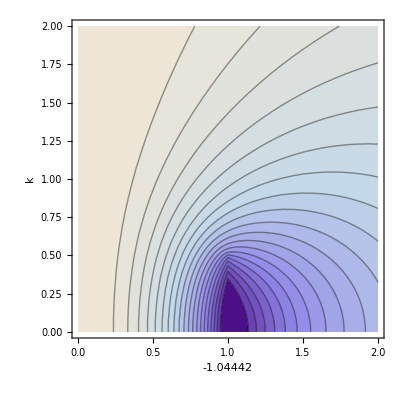

```mathematica
ContourPlot[MutualL[1,1,R,k],{R,0,2},{k,0,2},Contours->Table[-0.5 n,{n,0,20}],FrameLabel->Automatic]
```

```mathematica
Clear[R]
```

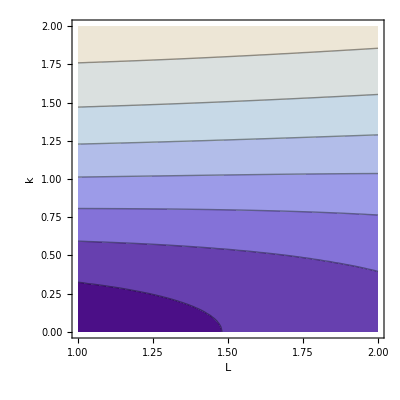

```mathematica
ContourPlot[MutualL[1,L,2,k],{L,1,2},{k,0,2},Contours->Table[-0.5 n,{n,0,20}],FrameLabel->Automatic]
```

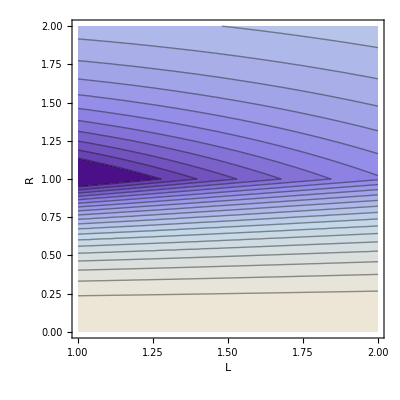

```mathematica
ContourPlot[MutualL[1,L,R,0],{L,1,2},{R,0,2},Contours->Table[-0.5 n,{n,0,20}],FrameLabel->Automatic]
```

```mathematica
ContourPlot3D[2π R AϕL[1,L,R,k],{L,1,2},{R,0,2},{k,0,2}]
```

$Aborted